## Setup

This setup uses (n,η) variables instead of (ρ,η).

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->100,"BC"->"Reflective"}];
runTwoComponentSim[{fhat_,uSource_,vSource_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]
+(eps (uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Eqs"->{
Dv discreteLaplace[etaVec,L/gridRes]
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
Dv (1+Du/Dv) discreteLaplace[etaVec,L/gridRes]
-Du discreteLaplace[nVec,L/gridRes]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Jacobian

```mathematica
laplaceMatrixAS[n_?NumericQ]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]*n^2;
```

```mathematica
laplaceMatrixS[n_?NumericQ]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]*n^2;
```

```mathematica
ClearAll@constructGluedJacobian;
Options@constructGluedJacobian={"Reverse"->False,"Symmetric"->False};
constructGluedJacobian[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@fdSetup["UnitGrid"],
grid
},
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{0,Dv},{-Du,(Du+Dv)}}/L^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
];
```

## Source terms (s_1,s_2)=(p-n,0)

### Model setup

Cubic reaction kinetics in (n,η) variables

```mathematica
f=η-n^3+n; (*\tilde{f}*)
source=p-n;
```

```mathematica
fixedParams={p->-0.2,Du->1,L->15,T->10000};
params=Join[{eps->0.001,Dv->10},fixedParams];
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[{f,source,0},100];
```

## Stationary state

```mathematica
initRun=runTwoComponentSim[
{f,source,0},
params,
{
0.5Cos[Pi#/L]&,
0&
},
T/.fixedParams
];
```

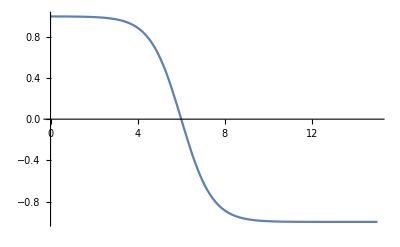

```mathematica
Plot[n[x,T/.params]/.initRun,{x,0,L/.params}]
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun]
]
];
```

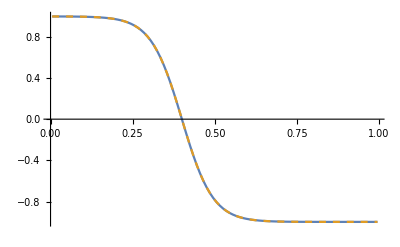

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.params/.initRun}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.statSol}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

## Linear stability analysis

#### Analytic expression for growth rate in diff- and react-limited regimes (Appendix H1)

```mathematica
σR=48/(1+Du/Dv) Exp[-2ξ L/√(Du/2)]/.ξ->(p+1)/2;
σD=8 Dv/(√(Du/2) L(1-ξ))Exp[-2ξ L/√(Du/2)]/.ξ->(p+1)/2;
```

## Numerics

### D_v-sweep

Note: the stationary state for the cubic model is independent of D_v. Therefore, one can use the same stationary-state solution as initial guess for all D_v.

```mathematica
DvEpsSweep[L->15]=Monitor[
Block[{paramsL,iniSol,sol,discSol,epsCritTheory,TOL},
Table[
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];

iniSol=runTwoComponentSim[
{f,source,0},
paramsL,
{
(n[#,T]/.initRun/.params)&,
(eta[#,T]/.initRun/.params)&
},
T/.fixedParams
];
discSol=n[x*L,T]/.params/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
 I,
iniSol
},
(*test for (half) pattern having two mesas*)
If[(discSol[[1]]<0||Length@Select[FindPeaks[discSol],#[[2]]>0&]>1),
PrintTemporary["Mesa splitted!"];
{
{DvIter,epsIter},
 2I,
 2I,
iniSol
},
sol=Quiet[Check[FindRoot[
fdSetup["Eqs"]/.paramsL,
getInitGuess[fdSetup,paramsL,iniSol]
],3I,FindRoot::cvmit],FindRoot::cvmit];

If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I,
sol
},
{
{DvIter,epsIter},
Eigenvalues[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps source,-f+Du/Dv eps source},{{n,η}}],(*reaction + source terms in n and eta*)
"Reverse"->False,
"Symmetric"->False
]][[-1]],
SortBy[Eigenvalues[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps source,-f+Du/Dv eps source},{{n,η}}],
"Reverse"->False,
"Symmetric"->True
]][[-2;;]],Abs[#]&][[-1]],
sol
}]]],
{DvIter,10^Range[2/10,6,2/10]},{epsIter,10^Range[-7,0,2/10]}
]],
{N@{epsIter,DvIter},
Plot[n[x,T]/.iniSol/.params,{x,0,L/.params}]}
];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{249.767,Null}

### Improved approximation of the stability threshold by shifting all source terms into v and explicitly accounting for the nullcline deformation induced by the u-sources [solving Eq. (H5)]

```mathematica
epsCorr=Table[Block[{dd},
dd=FindRoot[1==(2L √(Du/(2(1-eps)))(√(1-eps)-p)/(2 √(1-eps)))/(16Dv(1-eps))Exp[(2L(√(1-eps)+p)/(2 √(1-eps)))/(√(Du/(2(1-eps))))]eps(√(1-eps)-p)/(2 √(1-eps))/.fixedParams,{Dv,10}];
{Dv/.dd,eps}]
,{eps,10^Range[-7,-0.01,0.01]}]/.fixedParams;
```

## Plots

### Stability regions

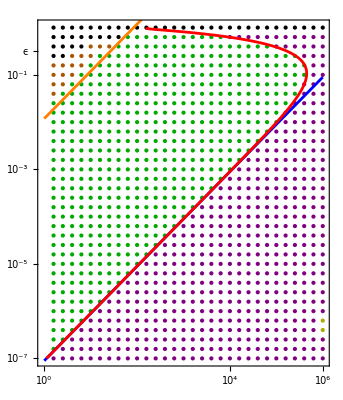

```mathematica
Graphics[{
(*single-domain instability, non-oscillatory*)
Darker@Red,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]==0&&Re[#[[3]]]>0&][[All,1]]],
(*single-domain instability, oscillatory*)
Darker@Blue,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]≠0&&Re[#[[3]]]>0&][[All,1]]],
(*mass-competition instability*)
Purple,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[3]]]<0&&Re[#[[2]]]<0&][[All,1]]],
(*NDSolve mesa splitting*)
Darker@Orange,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],


AbsoluteThickness[2],
Blue,(*threshold, Eq. (47)*)
Line[{{0,Log10[σD 2/(1-p)]/.Dv->1},{6,Log10[σD 2/(1-p)]/.Dv->10^6}}/.params],
Red,(*improved threshold Eq. (H5)*)
Line[Log10@epsCorr],
Orange,(*mesa splitting, Eq. (H6)*)
Line[{{0,Log10[64/(3Sqrt[3]*(1-p)^2*(1+p)*(2L)^2)*Dv]/.Dv->1},{6,Log10[64/(3Sqrt[3]*(1-p)^2*(1+p)*(2L)^2)*Dv]/.Dv->10^6}}/.params]
},
PlotRange->{{-0.02,6.02},{-7.02,0.02}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-0.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
{{0,"10^0",{0,0.02}},{2,"10^2",{0,0.02}},{4,"10^4",{0,0.02}},{5.5,"Dv",{0,0}},{6,"10^6",{0,0.02}}},
None
}
}
]
```

### Profiles

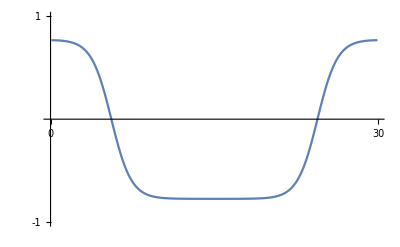

```mathematica
logD=5.6;
logEps=-0.4;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}},
PlotRange->{-1,1}]
```

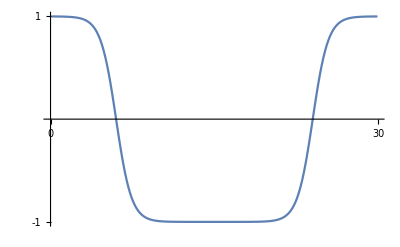

```mathematica
logD=5.6;
logEps=-6.6;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}}]
```

```mathematica
logD=0.4;
logEps=-6.6;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}}]
```

-Graphics-

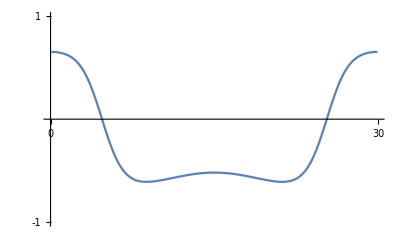

```mathematica
logD=1.6;
logEps=-0.4;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}},
PlotRange->{-1,1}]
```

### Growth rates

#### σ(D_v) at ϵ=10^-3

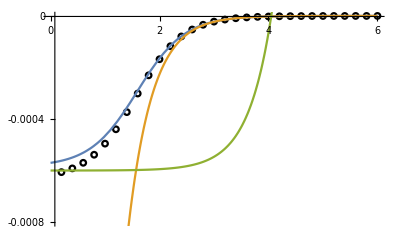

```mathematica
Show[
ListPlot[{
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->15][[All,21]]
},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[
Evaluate[{(1-eps (1-p)/2/σD)/(1/σD+1/σR),(1-eps (1-p)/2/σD)/(1/σR),σD-eps (1-p)/2 }/.eps->10^-3/.Dv->10^x/.params],{x,0,6},
PlotRange->All
],
PlotRange->{-8 10^-4,0},
Ticks->{{0,2,4,6},{-0.0008,-0.0004,0}}
]
```

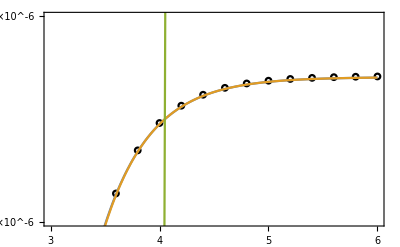

```mathematica
Show[
ListPlot[{
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->15][[All,21]]
},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[
Evaluate[{(1-eps (1-p)/2/σD)/(1/σD+1/σR),(1-eps (1-p)/2/σD)/(1/σR),σD-eps (1-p)/2 }/.eps->10^-3/.Dv->10^x/.params],{x,0,6},
PlotRange->All
],
Frame->True,
PlotRange->{{3,6},{- 0.5*10^-5,0.5*10^-5}},
FrameTicks->{{{-0.5*10^-5,0.5*10^-5},None},{{3,4,5,6},None}}
]
```

#### σ(D_v) at ϵ=10^-5

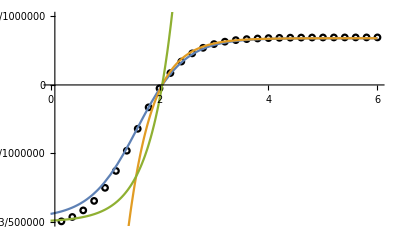

```mathematica
Show[
ListPlot[{
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->15][[All,11]]
},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[
Evaluate[{(1-eps (1-p)/2/σD)/(1/σD+1/σR),(1-eps (1-p)/2/σD)/(1/σR),σD-eps (1-p)/2 }/.eps->10^-5/.Dv->10^x/.params],{x,0,6},
PlotRange->All
],
PlotRange->{-6*10^-6,3*10^-6},
Ticks->{{0,2,4,6},{-6*10^-6,-3*10^-6,0,3*10^-6}}
]
```

## Source terms (s_1,s_2)=(0,p-n)

### Model setup

Cubic reaction kinetics in (n,η) variables

```mathematica
f=η-n^3+n;(*\tilde{f}*)
source=p-n;
```

```mathematica
fixedParams={p->-0.2,Dv->10,Du->1,L->15,T->10000};
params=Join[{eps->0.001,Dv->10},fixedParams];
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[{f,0,source},100];
```

## Stationary state

```mathematica
initRun=runTwoComponentSim[
{f,0,source},
params,
{
0.5Cos[Pi#/L]&,
0&
},
T/.fixedParams
];
```

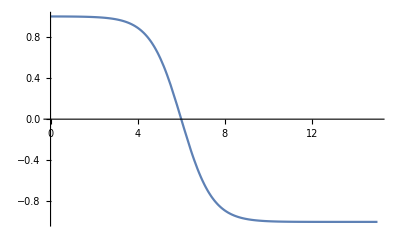

```mathematica
Plot[n[x,T/.params]/.initRun,{x,0,L/.params}]
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun]
]
];
```

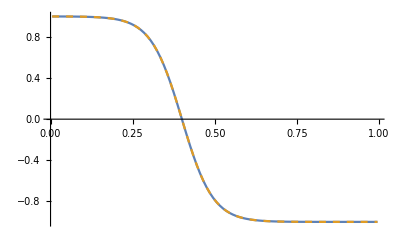

```mathematica
ListLinePlot[{
Transpose[{x,n[L x,T]/.params/.initRun}/.x->fdSetup["UnitGrid"]],
Transpose[{fdSetup["UnitGrid"],fdSetup["nVec"]/.statSol}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

## Linear stability analysis

#### Analytic expression for growth rate in diff- and react-limited regimes (Appendix H1)

```mathematica
σR=48/(1+Du/Dv) Exp[-2ξ L/√(Du/2)]/.ξ->(p+1)/2;
σD=8 Dv/(√(Du/2) L(1-ξ))Exp[-2ξ L/√(Du/2)]/.ξ->(p+1)/2;
```

## Numerics

### D_v-sweep

Note: the stationary state for the cubic model is independent of D_v. Therefore, one can use the same stationary-state solution as initial guess for all D_v.

```mathematica
DvEpsSweep[L->15]=Monitor[
Block[{paramsL,iniSol,sol,discSol,epsCritTheory},
Table[
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];
iniSol=Quiet[runTwoComponentSim[
{f,0,source},
paramsL,
{
Interpolation[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
discSol=n[x*L,T]/.params/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
 I,
iniSol
},
(*test for (half) pattern having two peaks*)
If[(discSol[[1]]<0||Length@Select[FindPeaks[discSol],#[[2]]>0&]>1),
PrintTemporary["Mesa splitted!"];
{
{DvIter,epsIter},
 2I,
 2I,
iniSol
},
sol=Quiet[Check[FindRoot[
fdSetup["Eqs"]/.paramsL,
getInitGuess[fdSetup,paramsL,iniSol](*statSol/.Rule->List*)
],3I,FindRoot::cvmit],FindRoot::cvmit];

If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I,
sol
},
{
{DvIter,epsIter},
Eigenvalues[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps source,-f+eps source},{{n,η}}],
"Reverse"->False,
"Symmetric"->False
]][[-1]],
SortBy[Eigenvalues[Normal@constructGluedJacobian[
fdSetup,
paramsL,
sol,
D[{eps source,-f+eps source},{{n,η}}],
"Reverse"->False,
"Symmetric"->True
]][[-2;;]],Abs[#]&][[-1]],
sol
}]]],
{DvIter,10^Range[2/10,6,2/10]},{epsIter,10^Range[-7,0,2/10]}
]],
N@{epsIter,DvIter}
];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{189.681,Null}

## Plots

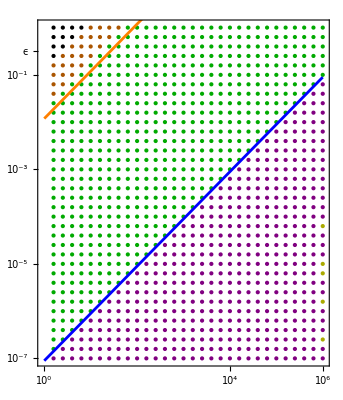

```mathematica
Graphics[{
(*single-domain instability, non-oscillatory*)
Darker@Red,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]==0&&Re[#[[3]]]>0&][[All,1]]],
(*single-domain instability, oscillatory*)
Darker@Blue,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]≠0&&Re[#[[3]]]>0&][[All,1]]],
(*mass-competition instability*)
Purple,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Re[#[[3]]]<0&&Re[#[[2]]]<0&][[All,1]]],
(*NDSolve mesa splitting*)
Darker@Orange,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[Log10@Select[Flatten[DvEpsSweep[L->15],1],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],

AbsoluteThickness[2],
Blue,(*threshold, Eq. (47)*)
Line[{{0,Log10[σD 2/(1-p)]/.Dv->1},{6,Log10[σD 2/(1-p)]/.Dv->10^6}}/.params],
Orange,(*improved threshold Eq. (H5)*)
Line[{{0,Log10[64/(3Sqrt[3]*(1-p)^2*(1+p)*(2L)^2)*Dv]/.Dv->1},{6,Log10[64/(3Sqrt[3]*(1-p)^2*(1+p)*(2L)^2)*Dv]/.Dv->10^6}}/.params]
},
PlotRange->{{-0.02,6.02},{-7.02,0.02}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-0.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
{{0,"10^0",{0,0.02}},{2,"10^2",{0,0.02}},{4,"10^4",{0,0.02}},{5.5,"Dv",{0,0}},{6,"10^6",{0,0.02}}},
None
}
}
]
```

### Profiles

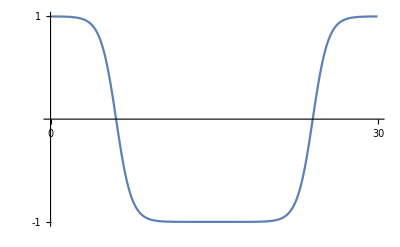

```mathematica
logD=5.6;
logEps=-0.4;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}}]
```

```mathematica
logD=5.6;
logEps=-6.6;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}}]
```

-Graphics-

```mathematica
logD=0.4;
logEps=-6.6;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}}]
```

-Graphics-

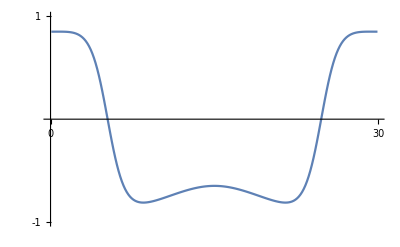

```mathematica
logD=1.4;
logEps=-0.4;
indD=First@First@Position[N[DvEpsSweep[L->15][[All,1,1,1]]],x_/;Abs[x-10^logD]<10^-7];
indEps=First@First@Position[N[DvEpsSweep[L->15][[1,All,1,2]]],x_/;Abs[x-10^logEps]<10^-7];
ListLinePlot[Join[Transpose@{L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]},Reverse@Transpose@{2L-L*fdSetup["UnitGrid"]/.params,fdSetup["nVec"]/.DvEpsSweep[L->15][[indD,indEps,-1]]}],
Ticks->{{0,2L/.params},{-1,1}},
PlotRange->{-1,1}]
```

### Growth rates

#### σ(D_v) at ϵ=10^-3

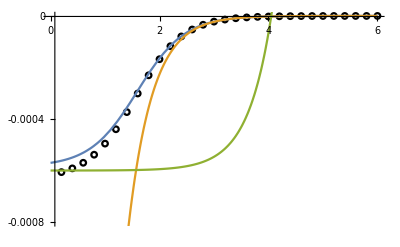

```mathematica
Show[
ListPlot[{
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->15][[All,21]]
},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[
Evaluate[{(1-eps (1-p)/2/σD)/(1/σD+1/σR),(1-eps (1-p)/2/σD)/(1/σR),σD-eps (1-p)/2 }/.eps->10^-3/.Dv->10^x/.params],{x,0,6},
PlotRange->All
],
PlotRange->{-8 10^-4,0},
Ticks->{{0,2,4,6},{-0.0008,-0.0004,0}}
]
```

Deviations at small Dv due to sharp-interface approx (for small Dv the gradient in eta is steeper and thus assuming eta as constant over the interface width is a worse approximation)

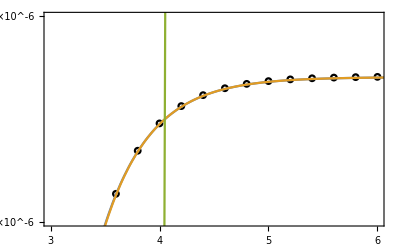

```mathematica
Show[
ListPlot[{
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->15][[All,21]]
},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[
Evaluate[{(1-eps (1-p)/2/σD)/(1/σD+1/σR),(1-eps (1-p)/2/σD)/(1/σR),σD-eps (1-p)/2 }/.eps->10^-3/.Dv->10^x/.params],{x,0,7},
PlotRange->All
],
Frame->True,
PlotRange->{{3,6},{- 0.5*10^-5,0.5*10^-5}},
FrameTicks->{{{-0.5*10^-5,0.5*10^-5},None},{{3,4,5,6},None}}
]
```

#### σ(D_v) at ϵ=10^-5

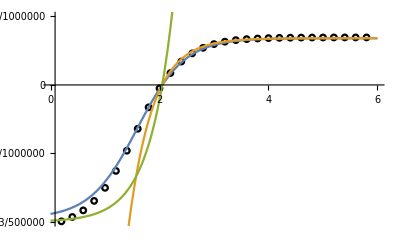

```mathematica
Show[
ListPlot[{
{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->15][[All,11]]
},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[
Evaluate[{(1-eps (1-p)/2/σD)/(1/σD+1/σR),(1-eps (1-p)/2/σD)/(1/σR),σD-eps (1-p)/2 }/.eps->10^-5/.Dv->10^x/.params],{x,0,6},
PlotRange->All
],
PlotRange->{-6*10^-6,3*10^-6},
Ticks->{{0,2,4,6},{-6*10^-6,-3*10^-6,0,3*10^-6}}
]
```